# RUN

```mathematica
airdat=Import["C:\\Users\\ricky\\Downloads\\NACA_0021.csv"];
```

```mathematica
dim=Dimensions[airdat]
```

{199,2}

```mathematica
mid=(dim[[1]]-1)/2+1
```

100

```mathematica
x=Table[airdat[[i,1]],{i,mid,dim[[1]]}]
```

{0,0.00019,0.00076,0.0017,0.00302,0.0047,0.00675,0.00915,0.01191,0.01502,0.01847,0.02227,0.02641,0.03088,0.03568,0.0408,0.04625,0.05201,0.05809,0.06447,0.07116,0.07814,0.08542,0.09299,0.10084,0.10897,0.11738,0.12605,0.13499,0.1442,0.15365,0.16336,0.17331,0.1835,0.19393,0.20458,0.21546,0.22656,0.23787,0.24938,0.2611,0.27301,0.28511,0.29739,0.30986,0.32249,0.33529,0.34824,0.36135,0.3746,0.38799,0.40152,0.41517,0.42893,0.44281,0.45679,0.47087,0.48503,0.49927,0.51359,0.52797,0.5424,0.55689,0.57141,0.58595,0.60052,0.6151,0.62968,0.64425,0.65879,0.67331,0.68778,0.7022,0.71655,0.73082,0.745,0.75907,0.77303,0.78685,0.80051,0.81401,0.82733,0.84043,0.85332,0.86596,0.87833,0.89041,0.90217,0.91358,0.92461,0.93521,0.94536,0.95499,0.96406,0.97248,0.98019,0.98705,0.99291,0.99748,1}

```mathematica
yt=Table[airdat[[i,2]],{i,mid,1,-1}]
```

{0,0.00428,0.00849,0.01264,0.01673,0.02075,0.0247,0.02858,0.03239,0.03613,0.0398,0.0434,0.04691,0.05035,0.05371,0.05698,0.06016,0.06326,0.06626,0.06917,0.07198,0.07469,0.0773,0.0798,0.0822,0.08448,0.08665,0.08871,0.09065,0.09248,0.09418,0.09576,0.09722,0.09856,0.09977,0.10086,0.10182,0.10265,0.10336,0.10394,0.1044,0.10473,0.10494,0.10503,0.10499,0.10483,0.10456,0.10416,0.10365,0.10303,0.1023,0.10145,0.1005,0.09945,0.0983,0.09704,0.0957,0.09426,0.09273,0.09111,0.08941,0.08763,0.08578,0.08385,0.08185,0.07978,0.07766,0.07547,0.07322,0.07092,0.06857,0.06618,0.06374,0.06127,0.05876,0.05621,0.05364,0.05105,0.04843,0.04581,0.04317,0.04052,0.03788,0.03524,0.03261,0.03,0.02741,0.02486,0.02235,0.0199,0.0175,0.01518,0.01296,0.01084,0.00885,0.00701,0.00536,0.00394,0.00282,0.0022}

```mathematica
yb=Table[airdat[[i,2]],{i,mid,dim[[1]]}]
```

{0,-0.00428,-0.00849,-0.01264,-0.01673,-0.02075,-0.0247,-0.02858,-0.03239,-0.03613,-0.0398,-0.0434,-0.04691,-0.05035,-0.05371,-0.05698,-0.06016,-0.06326,-0.06626,-0.06917,-0.07198,-0.07469,-0.0773,-0.0798,-0.0822,-0.08448,-0.08665,-0.08871,-0.09065,-0.09248,-0.09418,-0.09576,-0.09722,-0.09856,-0.09977,-0.10086,-0.10182,-0.10265,-0.10336,-0.10394,-0.1044,-0.10473,-0.10494,-0.10503,-0.10499,-0.10483,-0.10456,-0.10416,-0.10365,-0.10303,-0.1023,-0.10145,-0.1005,-0.09945,-0.0983,-0.09704,-0.0957,-0.09426,-0.09273,-0.09111,-0.08941,-0.08763,-0.08578,-0.08385,-0.08185,-0.07978,-0.07766,-0.07547,-0.07322,-0.07092,-0.06857,-0.06618,-0.06374,-0.06127,-0.05876,-0.05621,-0.05364,-0.05105,-0.04843,-0.04581,-0.04317,-0.04052,-0.03788,-0.03524,-0.03261,-0.03,-0.02741,-0.02486,-0.02235,-0.0199,-0.0175,-0.01518,-0.01296,-0.01084,-0.00885,-0.00701,-0.00536,-0.00394,-0.00282,-0.0022}

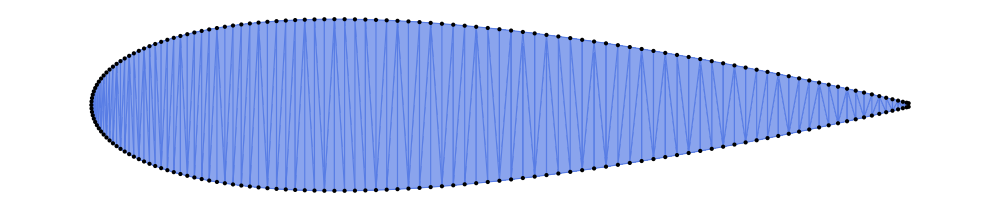

```mathematica
Show[DelaunayMesh[airdat,PlotTheme->"Business"],ImageSize->1000]
```

```mathematica
MomentOfInertia[DelaunayMesh[airdat]]
```

{{0.000364838,0.},{0.,0.00794057}}

```mathematica
(2.71*10^8)/(1.53*10^7)
```

17.7124

```mathematica
MomentOfInertia[DelaunayMesh[airdat]][[2,2]]/MomentOfInertia[DelaunayMesh[airdat]][[1,1]]
```

21.7646